```mathematica
Get[FindFile["JSONTools`"]]
```

```mathematica
(*-------------------------------------------------*)
(*     Verifica o Tamanho do Banco de Dados        *)
(*-------------------------------------------------*)

imp0=Import["http://www.echo1001.me:5003/node1/currentrms","json"];
dim=Dimensions[imp0[[1,2]]];
```

```mathematica
(*-------------------------------------------------*)
(*     Importa os Dados pela API (HISTÓRICO)       *)
(*-------------------------------------------------*)
(*     Dados do Experimento
	 
 Funcionamento Normal na Velocidade 1 9,77A = "2017-10-09 01:32:00" as "2017-10-09 01:33:00"
Funcionamento Normal na Velocidade 2 6,55A = "2017-10-09 01:34:00" as "2017-10-09 01:34:55"
Funcionamento Normal na Velocidade 3 4,82A = "2017-10-09 01:36:00" as "2017-10-09 01:37:00"

  Funcionamento Anormal na Velocidade 1     = "2017-10-09 01:41:00" as "2017-10-09 01:41:30"
 Funcionamento Anormal na Velocidade 1     = "2017-10-09 01:43:00" as "2017-10-09 01:43:30"
Funcionamento Anormal na Velocidade 1     = "2017-10-09 01:45:00" as "2017-10-09 01:45:30"

Funcionamento Normal na Velocidade 1 Continuo = "2017-10-09 01:47:00" as "2017-10-09 01:50:00"

*)
(*-------------------------------------------------*)
(*     Datas e Horarios de Inicio e Fim do Evento  *)

init = "2017-10-09 01:41:00";
end = "2017-10-09 01:41:30";
init = StringReplace[init,Whitespace->"%20"];
end = StringReplace[end,Whitespace->"%20"];

(* Importa em RawJSON *)
imp = Import["http://www.echo1001.me:5003/node1/currentrms/"<>init<>"/"<>end,"RawJSON"];

(* Converte *)
date  = imp[[1,;;,1]];
current = imp[[1,;;,2]];

current=ToExpression/@current;
```

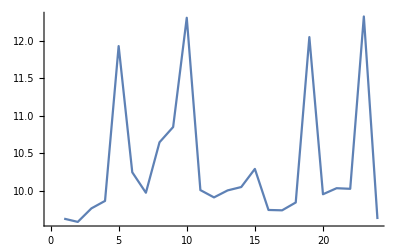

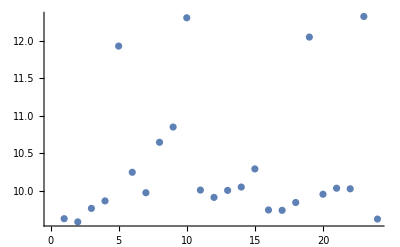

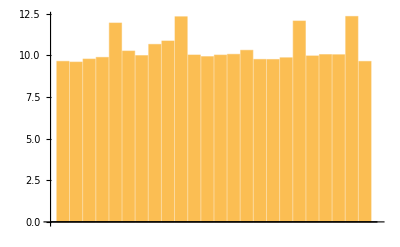

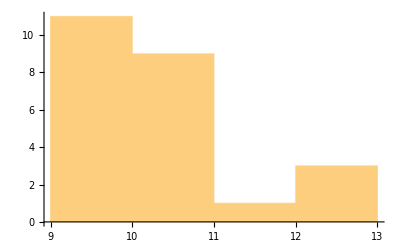

```mathematica
(* Plot dos Dados *)
ListLinePlot[current]
ListPlot[current]
BarChart[current]
Histogram[current]
```

```mathematica
(*---------------------------------------------------*)
(*---------------------------------------------------*)
(*     Importa os Dados pela API (INSTANTÂNEO)       *)
(*---------------------------------------------------*)
(*---------------------------------------------------*)
(* Coleta o ultimo valor instantaneo que a API envia *)

(*instantAPI[]:=Module[{n},*)

(* Liga o Motor*)
URLFetch["http://www.echo1001.me:5003/node1/comand/liga",Method->"POST"];
(*Pause[3];*)

list=List[{0}];
sizelist=1;
sizeloop=1;
stop=1;

While[sizeloop<10,

While[sizelist≤ 5,

(* Importa todos os Valores do JSON *)
imp = Import["http://www.echo1001.me:5003/node1/currentrms/instant","RawJSON"];
(* Seleciona Somente a Corrente *)
current = imp[[1,;;,2]];

(* Verifica se o valor é diferente o anterior *)
If[current!=Last[list],

(* Se sim, adiciona na lista *)
list=Append[list,current];
(* Retira o Zero Inicial da Lista *)
If[sizelist== 1,
list = Drop[list,1];
];

sizelist++;

]
];


(* Repassa a Lista para o Calculo *)
case =list;


   (*---------------------------------------------------*)
(*     Calculo de Média de Variancia                 *)
(*---------------------------------------------------*)

casemean = ToExpression/@case;
casevariance = ToExpression/@case;
casemean = Mean[casemean];
casevariance = Variance[casevariance];

(*---------------------------------------------------*)
(*     Resultado do Teste                            *)
(*---------------------------------------------------*)

(*Plot[c[x,{"Probability","NORMAL"}],{x,0,1},Exclusions->None]*)
c[casevariance,"Probabilities"];
c[casevariance];
If[c[casevariance]!={"NORMAL"},
URLFetch["http://www.echo1001.me:5003/node1/comand/desl",Method->"POST"];

If[stop==1,SendMail["To"-> "eng.edgar.reis@gmail.com", "Subject"-> "Motor em Falha!!!", "Body"-> {"Motor em Falha! Corrente: ", case[[3]], BarChart[ToExpression/@case],""},"From"->"eng.edgar.reis@gmail.com","Server"->"smtp.gmail.com","UserName"->"eng.edgar.reis@gmail.com","Password"->Automatic,"PortNumber"->587,"EncryptionProtocol"->"StartTLS"];stop++];

];


(* Preparo para o proximo loop *)

(* Retira o primeiro elemento da lista *)
list = Drop[list,1];
(* Referencia a retirada *)
sizelist--;
(* Imcremento para o loop *)
sizeloop++;

Print["Variância: ",casevariance,"  |  Corrente: ",case,"  |  Verificação: ",c[casevariance]];

]
```

Variância: {0.00381132}  |  Corrente: {{9.8436367207},{9.7899217843},{9.9130601124}}  |  Verificação: {NORMAL}

Variância: {0.00383618}  |  Corrente: {{9.7899217843},{9.9130601124},{9.8398178895}}  |  Verificação: {NORMAL}

Variância: {0.00134116}  |  Corrente: {{9.9130601124},{9.8398178895},{9.8760332420}}  |  Verificação: {NORMAL}

Variância: {0.00350507}  |  Corrente: {{9.8398178895},{9.8760332420},{9.7602958766}}  |  Verificação: {NORMAL}

Variância: {0.00335013}  |  Corrente: {{9.8760332420},{9.7602958766},{9.8161582234}}  |  Verificação: {NORMAL}

Variância: {0.00632525}  |  Corrente: {{9.7602958766},{9.8161582234},{9.9172049468}}  |  Verificação: {NORMAL}

Variância: {0.969683}  |  Corrente: {{9.8161582234},{9.9172049468},{11.5700288848}}  |  Verificação: {ANORMAL}

Variância: {39.1996}  |  Corrente: {{9.9172049468},{11.5700288848},{-0.0057971804}}  |  Verificação: {ANORMAL}

Variância: {0.0004904}  |  Corrente: {{6.7212398202},{6.6773835356},{6.7046659710}}  |  Verificação: {NORMAL}

Variância: {0.00213883}  |  Corrente: {{6.6773835356},{6.7046659710},{6.7675638211}}  |  Verificação: {NORMAL}

Variância: {0.00172271}  |  Corrente: {{6.7046659710},{6.7675638211},{6.6891996776}}  |  Verificação: {NORMAL}

Variância: {0.00259575}  |  Corrente: {{6.7675638211},{6.6891996776},{6.6719765812}}  |  Verificação: {NORMAL}

Variância: {2.29807}  |  Corrente: {{6.6891996776},{6.6719765812},{9.3062270309}}  |  Verificação: {ANORMAL}

Variância: {22.9953}  |  Corrente: {{6.6719765812},{9.3062270309},{0.0027718084}}  |  Verificação: {ANORMAL}

Variância: {28.8583}  |  Corrente: {{9.3062270309},{0.0027718084},{0.0005526014}}  |  Verificação: {ANORMAL}

Variância: {1.59966×10^-6}  |  Corrente: {{0.0027718084},{0.0005526014},{0.0006108662}}  |  Verificação: {NORMAL}

Variância: {1.80864×10^-9}  |  Corrente: {{0.0005526014},{0.0006108662},{0.0005280698}}  |  Verificação: {NORMAL}

Variância: {1.5839}  |  Corrente: {{4.5192439436},{6.6627652099},{6.7336671089}}  |  Verificação: {ANORMAL}

Variância: {14.9538}  |  Corrente: {{6.6627652099},{6.7336671089},{0.0006267642}}  |  Verificação: {ANORMAL}

Variância: {15.1108}  |  Corrente: {{6.7336671089},{0.0006267642},{0.0008269203}}  |  Verificação: {ANORMAL}

Variância: {2.02172×10^-8}  |  Corrente: {{0.0006267642},{0.0008269203},{0.0009017841}}  |  Verificação: {NORMAL}

Variância: {6.60708×10^-7}  |  Corrente: {{0.0008269203},{0.0009017841},{-0.0005420334}}  |  Verificação: {NORMAL}

Variância: {8.5392×10^-7}  |  Corrente: {{0.0009017841},{-0.0005420334},{0.0011790262}}  |  Verificação: {NORMAL}

Variância: {7.41225×10^-7}  |  Corrente: {{-0.0005420334},{0.0011790262},{0.0002722431}}  |  Verificação: {NORMAL}

Variância: {2.14213×10^-7}  |  Corrente: {{0.0011790262},{0.0002722431},{0.0008867200}}  |  Verificação: {NORMAL}

Variância: {9.43966×10^-8}  |  Corrente: {{0.0002722431},{0.0008867200},{0.0005776162}}  |  Verificação: {NORMAL}

Variância: {44.673}  |  Corrente: {{11.5700288848},{-0.0057971804},{-0.0074613018}}  |  Verificação: {ANORMAL}

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
" case[[1]]"
```

{-0.0086696528}

```mathematica
BarChart[ToExpression/@case];
```

```mathematica
SendMail["To"-> "eng.edgar.reis@gmail.com", "Subject"-> "Motor em Falha!!!", "Body"-> {"Motor em Falha! Corrente: ", BarChart[ToExpression/@case],""},"From"->"eng.edgar.reis@gmail.com","Server"->"smtp.gmail.com","UserName"->"eng.edgar.reis@gmail.com","Password"->Automatic,"PortNumber"->587,"EncryptionProtocol"->"StartTLS"];
```

```mathematica
While[True,
Print["."];
If[Input[]==1,Break[]]]
```

```mathematica
URLFetch["http://www.echo1001.me:5003/node1/comand/liga",Method->"POST"]
```

"ON"

```mathematica
URLFetch["http://www.echo1001.me:5003/node1/comand/desl",Method->"POST"]
```

"OFF"

```mathematica
BarChart[ToExpression/@case];
```

```mathematica
RemoveScheduledTask[ScheduledTasks[]];
```

```mathematica
Head@x
```

Rational

```mathematica
ProgressIndicator[Dynamic[n],{100,140}]
```

```mathematica
PopupWindow[teste,"Label"]
```

teste

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
(* Classify and Train (Baseado nos Dados Coletados http://reference.wolfram.com/language/ref/Classify.html *)
(*---------------------------------------------------------------------------------------------------------*)

(*---------------------------------------------------*)
(*     Dados Pré Processados                         *)
(*---------------------------------------------------*)
normal={"9.8451735939","9.7875107359","9.7583907850","9.7436997438","9.8317609564","9.8014133724","9.7198737348","9.8426881499","9.7374899635","9.7183666414","9.8321971807","9.7110343934","9.7622219651","9.8090033342","9.6839251437","9.8037321562","9.6743629742","9.8143016220","9.6781164858","9.6756981100","9.8064605647","9.6735369372","9.7845774503","9.7571540861","9.6616949587","9.8031859224","9.6593443350","9.7628688132","9.7289523845","9.6445536735","9.7451304464","9.7258050250","9.6366223649","9.6544516412","9.7671196502","9.6955180993","9.6344259501","9.7125327144","9.7183313623","9.6423319214","9.6308748880","9.7513775227","9.6541358542","9.6124402168","9.7332039844","9.6633904619","9.6116748018"};
anormal={"9.6299018103","9.5870709066","9.7670946949","9.8666182284","11.9291870806","10.2479733166","9.9755000993","10.6475587595","10.8508107894","12.3062974071","10.0107741579","9.9133955900","10.0065554097","10.0514695194","10.2927328785","9.7459689340","9.7412423259","9.8456998714","12.0489468206","9.9553326728","10.0357630666","10.0278111020","12.3236356907","9.6249220563"};
```

```mathematica
(*---------------------------------------------------*)
(*     Calculo de Média de Variancia                 *)
(*---------------------------------------------------*)
normalmean = ToExpression/@normal;
normalvariance = ToExpression/@normal;
normalmean = Mean[normalmean]
normalvariance = Variance[normalvariance]
(*---------------------------------------------------*)
anormalmean = ToExpression/@anormal;
anormalvariance = ToExpression/@anormal;
anormalmean = Mean[anormalmean]
anormalvariance = Variance[anormalvariance]
```

9.72559

0.00446826

10.3513

0.767672

```mathematica
(*---------------------------------------------------*)
(*     Treinamento e Classificação                   *)
(*---------------------------------------------------*)
trainingset={normalvariance->"NORMAL", anormalvariance->"ANORMAL"};
c=Classify[trainingset]
```

ClassifierFunction[…]

```mathematica
(*---------------------------------------------------*)
(*     Caso para Teste  (Opção 1 - Import)           *)
(*---------------------------------------------------*)
(*case=imp[[1,;;,2]]*)
case=list
```

{{22},{32},{16}}

```mathematica
(*---------------------------------------------------*)
(*     Caso para Teste (Opção 2 - Normal)            *)
(*---------------------------------------------------*)

case={"9.3841840524","9.4417007675","9.3692330472","9.2984841906","9.3720028873","9.3082597508","9.3999327684","9.4115148685","9.3054939659","9.4312011857","9.3462801245","9.3056241556","9.4219056886","9.3452236103","9.3433537399","9.4117101091","9.4233899202","9.3290883392","9.2951500145","9.3922445080","9.3852543583","9.3691411348","9.3948547253","9.3083249466","9.2781042048","9.3796321535","9.3712665510","9.2781278815","9.3636873463","9.4087059042","9.3491224406","9.3050991457","9.2724305892","9.3395444378","9.2835630846","9.3416626446","9.4003723466","9.3109590623","9.2673519173","9.3448511937","9.3779305343","9.2766515535","9.3131591033","9.3921508932","9.3223282728","9.3323059460","9.3832140598","9.2890415767","9.2621092324","9.3527898728","9.3781159658","9.2833220216","9.2678164524","9.3595629345","9.3639608848","9.2506465798","9.3581621981","9.3821907498","9.2960448975","9.2457301100","9.3165948213","9.3702319473","9.3134054001","9.2568122715","9.2538179447","9.3793718307","9.2407693791","9.3464862170","9.3423424693","9.2803356473","9.2436872964","9.3319430658","9.3594135350","9.2599541467","9.2428230825","9.3251956706","9.3683325725","9.2808536630","9.2372638397","9.3095376434","9.3431059450","9.2361173946","9.2992962220","9.3670878432","9.2618953398","9.2629889042","9.2952845657","9.3289710727","9.3424610891","9.2304915693","9.3321374802","9.3360001800","9.2879475419","9.2249687729","9.2264630567","9.3462595856","9.3122762582","9.2701630893","9.3266689899","9.2572254686","9.2187222649","9.2304957296","9.2474785644","9.3199309158","9.3441278402","9.3090948991","9.2760761405","9.2192276140","9.3493668349","9.2518591053","9.2479061707","9.3365726705","9.2832381050","9.2887836204","9.3410910260","9.2339719239","9.2823464252","9.3441492498","9.2703030634","9.3275703010","9.2267919720","9.2226654949","9.3331108449","9.2898044572","9.2951446569","9.3039112823","9.1981184143","9.3083477745","9.2780861868","9.2047752433","9.2422557399","9.2274266636","9.2856761188","9.3039683978","9.1902273971","9.2345175735","9.2790250331","9.2082790152","9.2115982757","9.2109681383","9.2942321847","9.2075597898"}
```

```mathematica
(*---------------------------------------------------*)
(*     Calculo de Média de Variancia                 *)
(*---------------------------------------------------*)

casemean = ToExpression/@case;
casevariance = ToExpression/@case;
casemean = Mean[casemean]
casevariance = Variance[casevariance]
```

10.3513

0.767672

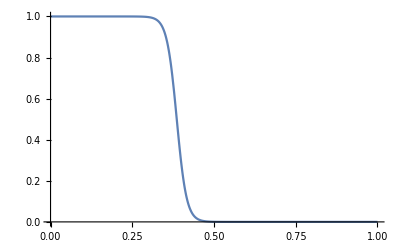

<|ANORMAL→1.,NORMAL→1.00222×10^-11|>

ANORMAL

```mathematica
(*---------------------------------------------------*)
(*     Resultado do Teste                            *)
(*---------------------------------------------------*)

Plot[c[x,{"Probability","NORMAL"}],{x,0,1},Exclusions->None]
c[casevariance,"Probabilities"]
c[casevariance]
```

```mathematica
(*---------------------------------------------------*)
(*     Envia Comando Para Atuação                    *)
(*     POST -> API -> SQLite -> MQTT -> Node            *)
(*---------------------------------------------------*)
```

```mathematica
(* Topico:cmd/node1/rele1 *)
URLFetch["http://www.echo1001.me:5003/node1/comand/liga",Method->"POST"]
```

"ON"

```mathematica
(* Topico:cmd/node1/rele1 *)
URLFetch["http://www.echo1001.me:5003/node1/comand/desl",Method->"POST"]
```

"OFF"